```mathematica
Needs["ExperimentEvaluation`"]
SetDirectory["~"];
solverRewrite={"SOLVER",{"GP"->"G","NEAT"->"N"}};
distanceRewrite={"GP.DISTANCE",{"GENERAL"->"G","BASIC"->"I","ISO"->"D","PHENO"->"P","RANDOM"->"R","NODES"->"N","Null"->""}};
plotRange={All,{0,100}};
```

## OCTOPUS BSF

```mathematica
Needs["PlotLegends`"]
readRunFitness[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
noHeaderData = Rest[allData];
data = noHeaderData⟦All,2;;⟧;
{data,noHeaderData⟦All,1⟧, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
readRunEvaluationInfo[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
data = Rest[allData];
{data,Max/@data, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
enlarge[list_, fill_, stat_]:=list~Join~Array[fill&,Max[Length/@stat]-Length[list]]
enlarge[list_, fill_, stat_, len_]:=list~Join~Array[fill&,len-Length[list]]
enlarge[list_,bsfAvg_]:=list~Join~Array[Max[bsfAvg]&,Max[Length/@bsfAvg]-Length[list]]
```

```mathematica
bsfAvgGP = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/GP_OCTOPUS"}]);
(*bsfAvgBASIC = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_BASIC_GECCO"}]);
bsfAvgGENERAL = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_GENERAL_GECCO"}]);
bsfAvgISO = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_ISO_GECCO"}]);
bsfAvgNODES = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_NODES_GECCO"}]);
bsfAvgPHENO = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_PHENO_GECCO"}]);
bsfAvgRANDOM = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_RANDOM_GECCO"}]);*)
bsfAvgGPEFSG = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/GPEFS_OCTOPUS_GENERAL"}]);
bsfAvgANJI = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/ANJI_OCTOPUS"}]);
bsfAvgNEAT = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/NEAT_OCTOPUS"}]);
```

```mathematica
maxGenerations=Max@@(Max[Length[#]&/@#]&/@{bsfAvgGP,bsfAvgNEAT})
```

500

```mathematica
bsfAvgGP=Mean[bsfAvgGP];
(*bsfAvgBASIC=Mean[(enlarge/@bsfAvgBASIC)];
bsfAvgGENERAL=Mean[(enlarge/@bsfAvgGENERAL)];
bsfAvgISO=Mean[(enlarge/@bsfAvgISO)];
bsfAvgNODES=Mean[(enlarge/@bsfAvgNODES)];
bsfAvgPHENO=Mean[(enlarge/@bsfAvgPHENO)];
bsfAvgRANDOM=Mean[(enlarge/@bsfAvgRANDOM)];*)
bsfAvgGPEFSG=Mean[bsfAvgGPEFSG];
bsfAvgANJI=Mean[bsfAvgANJI];
bsfAvgNEAT=Mean[bsfAvgNEAT];
```

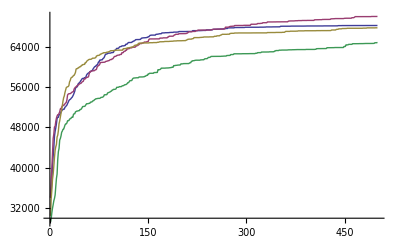

```mathematica
ListLinePlot[{bsfAvgGP,bsfAvgGPEFSG,bsfAvgANJI,bsfAvgNEAT}, PlotRange->All]
```

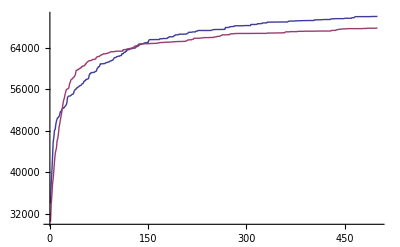

```mathematica
ListLinePlot[{bsfAvgGPEFSG,bsfAvgANJI}, PlotRange->All]
```